### Categorization

Tutorial

HeatTrans Package

HeatTrans`

HeatTrans/tutorial/Validation

### Keywords

Details

# Validation tutorial

This tutorial describes validation of heat transfer model.

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

Load the package:

```mathematica
Needs["HeatTrans`"]
```

Define 2D region, time and material properties.

```mathematica
region=Disk[{0,0},1/20];
endTime=60;
material=<|"Conductivity"->50,"Density"->7800,"SpecificHeat"->470|>;
```

Use HeatTransfer function.

```mathematica
result=HeatTransfer[region,endTime,material,"NoTimeSteps"->60]
```

```mathematica
Options@HeatTransfer
```

{AmbientTemperature→20.,Console→Automatic,ConvectionCoefficient→20.,InitialTemperature→100.,MeshOrder→1,NoTimeSteps→Automatic,SaveResultsTo→False}

Pull mesh representation from InterpolatingFunction object

```mathematica
mesh=result["ElementMesh"]
```

Solve the same problem with NDSolveValue function.

```mathematica
solMMA=With[{
ρ=material["Density"],
cp=material["SpecificHeat"],
k=material["Conductivity"],
h=20.,
Ti=100.,
Ta=20.
},
NDSolveValue[{
ρ*cp*D[u[t,x,y],t]-k*Laplacian[u[t,x,y],{x,y}]==NeumannValue[h*(Ta-u[t,x,y]), True],
u[0,x,y]==Ti
},
u,
{t,0,endTime},
{x,y}∈mesh,
MaxStepSize->1.
]
]
```

Curves of temperature versus time, calculated with HeatTransfer and NDSolveValue, overlap almost completely.

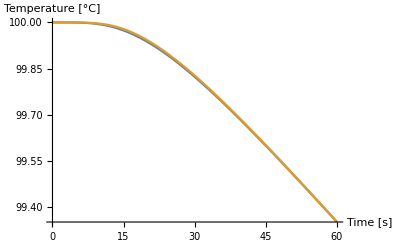

```mathematica
Plot[
{result[t,0,0],solMMA[t,0,0]},
{t,0,endTime},
AxesLabel->{"Time [s]","Temperature [°C]"}
]
```

More About

Related Tutorials

Related Wolfram Education Group Courses